## Use Stirling Numbers to Define Chromatic Polynomials

```mathematica
chromaticPolynomial[n_]:=Simplify[FunctionExpand[Sum[Sum[StirlingS2[n,i]*StirlingS2[n,j]*FactorialPower[q,i+j],{j,1,n}],{i,1,n}]]]
```

```mathematica
chromaticRoots[n_]:=N/@Solve[chromaticPolynomial[n]==0, q]
```

#### Magnitudes of Roots

```mathematica
(*try for n=10*)
Abs[q/.chromaticRoots[10]]
```

{0.,1.,2.,3.,4.00037,4.86746,5.25673,5.25673,5.81053,5.81053,6.51764,6.51764,7.43619,7.43619,8.64425,8.64425,10.2702,10.2702,12.6146,12.6146}

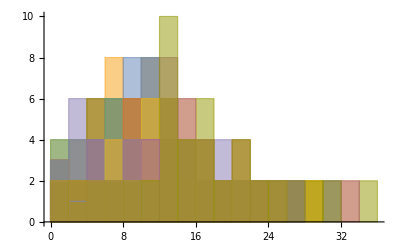

```mathematica
Histogram[Table[Abs[(q)/.chromaticRoots[n]],{n,1,25}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

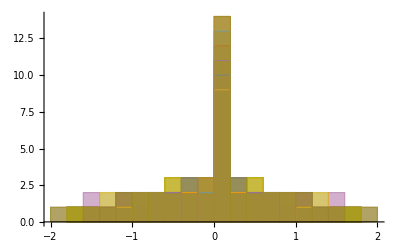

```mathematica
Histogram[Table[(Im[q]/Re[q])/.chromaticRoots[n],{n,1,25}]]
```

### Fitting Curves to Roots

```mathematica
filterRoots[roots_]:=Module[{newroots=List[]},
			For[i=1,i<=Length[roots], i++,If[Im[roots[[i]]]>0,AppendTo[newroots,roots[[i]]],0]];
Return[newroots]]
```

```mathematica
MapThread[List,{Re[Flatten[Table[filterRoots[(q/n)/.chromaticRoots[n]],{n,2,20}]]],Im[Flatten[Table[filterRoots[(q/n)/.chromaticRoots[n]],{n,2,20}]]]}]
```

{{0.75,0.433013},{0.619787,0.164045},{0.713547,0.649561},{0.535774,0.0393191},{0.638603,0.340307},{0.700622,0.774361},{0.590063,0.196832},{0.646877,0.466417},{0.693873,0.858237},{0.555994,0.114805},{0.60859,0.30877},{0.651674,0.560847},{0.689742,0.919445},{0.530795,0.0647865},{0.579303,0.212891},{0.619898,0.39761},{0.654825,0.634878},{0.686972,0.966538},{0.504844,0.0292997},{0.55598,0.148768},{0.594505,0.293596},{0.627613,0.470455},{0.657068,0.694849},{0.685001,1.00415},{0.536932,0.103212},{0.573567,0.221582},{0.605224,0.361873},{0.633231,0.531581},{0.658759,0.744643},{0.683537,1.03503},{0.521111,0.069105},{0.555961,0.168909},{0.586307,0.284676},{0.613212,0.420642},{0.637514,0.583787},{0.660089,0.786794},{0.682414,1.06094},{0.508788,0.0433958},{0.540958,0.128842},{0.570055,0.227018},{0.595989,0.340046},{0.619405,0.471909},{0.640896,0.629012},{0.661169,0.823037},{0.68153,1.08306},{0.495593,0.0242671},{0.52806,0.0974375},{0.555928,0.182383},{0.580951,0.278813},{0.603609,0.389146},{0.624352,0.517122},{0.64364,0.668652},{0.662069,0.854605},{0.680821,1.10222},{0.516905,0.0722859},{0.543543,0.146876},{0.567685,0.230741},{0.589642,0.325351},{0.609768,0.433064},{0.628401,0.55736},{0.645916,0.703743},{0.662835,0.8824},{0.680243,1.11899},{0.507051,0.0516228},{0.532614,0.118013},{0.555893,0.192037},{0.577178,0.274668},{0.596744,0.367456},{0.614855,0.472634},{0.63178,0.593452},{0.647838,0.735071},{0.663496,0.9071},{0.679764,1.13384},{0.49899,0.0343111},{0.52292,0.0941348},{0.545347,0.160244},{0.565979,0.23345},{0.585012,0.314792},{0.60266,0.405778},{0.619129,0.508513},{0.634645,0.626046},{0.649486,0.763247},{0.664076,0.929227},{0.679363,1.14709},{0.490975,0.0211104},{0.514286,0.0740748},{0.53587,0.133696},{0.55586,0.199295},{0.574378,0.271585},{0.591592,0.351619},{0.607667,0.440838},{0.622775,0.541225},{0.637109,0.655657},{0.650917,0.788753},{0.66459,0.949187},{0.679024,1.159},{0.506592,0.0570257},{0.527321,0.111221},{0.546678,0.170553},{0.564692,0.235511},{0.581487,0.306841},{0.597198,0.385569},{0.611963,0.473063},{0.625924,0.571197},{0.639252,0.682701},{0.652173,0.811974},{0.665051,0.967302},{0.678735,1.16978},{0.499588,0.0423687},{0.519584,0.0919691},{0.538314,0.146053},{0.555832,0.204951},{0.572218,0.269202},{0.587583,0.339552},{0.602035,0.416987},{0.61569,0.502803},{0.628673,0.59878},{0.641136,0.707518},{0.653287,0.833223},{0.665466,0.983833},{0.678487,1.17959},{0.493501,0.0293649},{0.512561,0.0753084},{0.530673,0.124938},{0.5477,0.178747},{0.563686,0.23713},{0.578712,0.30064},{0.59287,0.370004},{0.606252,0.446163},{0.618956,0.530352},{0.631095,0.624265},{0.642806,0.730389},{0.654281,0.852756},{0.665844,0.998992},{0.678272,1.18857},{0.488041,0.0189819},{0.506164,0.0607534},{0.523673,0.106565},{0.540216,0.156042},{0.555807,0.209484},{0.570502,0.267306},{0.584374,0.330055},{0.597501,0.398436},{0.609962,0.473345},{0.621844,0.555959},{0.633247,0.647898},{0.644298,0.751548},{0.655177,0.870786},{0.66619,1.01295},{0.678085,1.19682}}

```mathematica
test=FindFit[MapThread[List,{Re[Flatten[Table[filterRoots[(q/n)/.chromaticRoots[n]],{n,2,20}]]],Im[Flatten[Table[filterRoots[(q/n)/.chromaticRoots[n]],{n,2,20}]]]}],A*E^x+c,{A,c},x]
```

{A→2.88751,c→-4.8147}

```mathematica
A/.test
```

4.42346

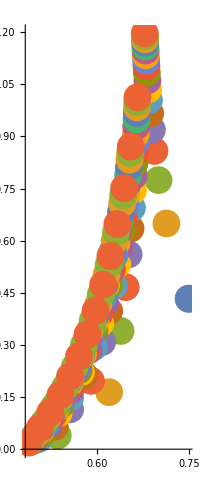

```mathematica
points=ComplexListPlot[Table[Flatten[filterRoots[(q/n)/.chromaticRoots[n]]],{n,2,20}], PlotStyle->PointSize[0.05]]
```

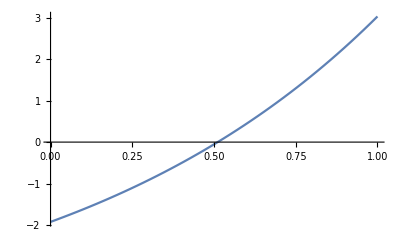

```mathematica
curve=Plot[(A/.test)*E^x+(c/.test),{x,0,1}]
```

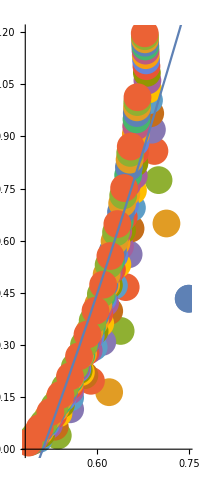

ComplexListPlot::lpn: {{},{{0.75,0.433013}},«8»,«10»} is not a list of numbers or pairs of numbers.

ComplexListPlot[{{},{0.75+0.433013 ⅈ},{0.619787+0.164045 ⅈ,0.713547+0.649561 ⅈ},{0.535774+0.0393191 ⅈ,0.638603+0.340307 ⅈ,0.700622+0.774361 ⅈ},{0.590063+0.196832 ⅈ,0.646877+0.466417 ⅈ,0.693873+0.858237 ⅈ},{0.555994+0.114805 ⅈ,0.60859+0.30877 ⅈ,0.651674+0.560847 ⅈ,0.689742+0.919445 ⅈ},{0.530795+0.0647865 ⅈ,0.579303+0.212891 ⅈ,0.619898+0.39761 ⅈ,0.654825+0.634878 ⅈ,0.686972+0.966538 ⅈ},{0.504844+0.0292997 ⅈ,0.55598+0.148768 ⅈ,0.594505+0.293596 ⅈ,0.627613+0.470455 ⅈ,0.657068+0.694849 ⅈ,0.685001+1.00415 ⅈ},{0.536932+0.103212 ⅈ,0.573567+0.221582 ⅈ,0.605224+0.361873 ⅈ,0.633231+0.531581 ⅈ,0.658759+0.744643 ⅈ,0.683537+1.03503 ⅈ},{0.521111+0.069105 ⅈ,0.555961+0.168909 ⅈ,0.586307+0.284676 ⅈ,0.613212+0.420642 ⅈ,0.637514+0.583787 ⅈ,0.660089+0.786794 ⅈ,0.682414+1.06094 ⅈ},{0.508788+0.0433958 ⅈ,0.540958+0.128842 ⅈ,0.570055+0.227018 ⅈ,0.595989+0.340046 ⅈ,0.619405+0.471909 ⅈ,0.640896+0.629012 ⅈ,0.661169+0.823037 ⅈ,0.68153+1.08306 ⅈ},{0.495593+0.0242671 ⅈ,0.52806+0.0974375 ⅈ,0.555928+0.182383 ⅈ,0.580951+0.278813 ⅈ,0.603609+0.389146 ⅈ,0.624352+0.517122 ⅈ,0.64364+0.668652 ⅈ,0.662069+0.854605 ⅈ,0.680821+1.10222 ⅈ},{0.516905+0.0722859 ⅈ,0.543543+0.146876 ⅈ,0.567685+0.230741 ⅈ,0.589642+0.325351 ⅈ,0.609768+0.433064 ⅈ,0.628401+0.55736 ⅈ,0.645916+0.703743 ⅈ,0.662835+0.8824 ⅈ,0.680243+1.11899 ⅈ},{0.507051+0.0516228 ⅈ,0.532614+0.118013 ⅈ,0.555893+0.192037 ⅈ,0.577178+0.274668 ⅈ,0.596744+0.367456 ⅈ,0.614855+0.472634 ⅈ,0.63178+0.593452 ⅈ,0.647838+0.735071 ⅈ,0.663496+0.9071 ⅈ,0.679764+1.13384 ⅈ},{0.49899+0.0343111 ⅈ,0.52292+0.0941348 ⅈ,0.545347+0.160244 ⅈ,0.565979+0.23345 ⅈ,0.585012+0.314792 ⅈ,0.60266+0.405778 ⅈ,0.619129+0.508513 ⅈ,0.634645+0.626046 ⅈ,0.649486+0.763247 ⅈ,0.664076+0.929227 ⅈ,0.679363+1.14709 ⅈ},{0.490975+0.0211104 ⅈ,0.514286+0.0740748 ⅈ,0.53587+0.133696 ⅈ,0.55586+0.199295 ⅈ,0.574378+0.271585 ⅈ,0.591592+0.351619 ⅈ,0.607667+0.440838 ⅈ,0.622775+0.541225 ⅈ,0.637109+0.655657 ⅈ,0.650917+0.788753 ⅈ,0.66459+0.949187 ⅈ,0.679024+1.159 ⅈ},{0.506592+0.0570257 ⅈ,0.527321+0.111221 ⅈ,0.546678+0.170553 ⅈ,0.564692+0.235511 ⅈ,0.581487+0.306841 ⅈ,0.597198+0.385569 ⅈ,0.611963+0.473063 ⅈ,0.625924+0.571197 ⅈ,0.639252+0.682701 ⅈ,0.652173+0.811974 ⅈ,0.665051+0.967302 ⅈ,0.678735+1.16978 ⅈ},{0.499588+0.0423687 ⅈ,0.519584+0.0919691 ⅈ,0.538314+0.146053 ⅈ,0.555832+0.204951 ⅈ,0.572218+0.269202 ⅈ,0.587583+0.339552 ⅈ,0.602035+0.416987 ⅈ,0.61569+0.502803 ⅈ,0.628673+0.59878 ⅈ,0.641136+0.707518 ⅈ,0.653287+0.833223 ⅈ,0.665466+0.983833 ⅈ,0.678487+1.17959 ⅈ},{0.493501+0.0293649 ⅈ,0.512561+0.0753084 ⅈ,0.530673+0.124938 ⅈ,0.5477+0.178747 ⅈ,0.563686+0.23713 ⅈ,0.578712+0.30064 ⅈ,0.59287+0.370004 ⅈ,0.606252+0.446163 ⅈ,0.618956+0.530352 ⅈ,0.631095+0.624265 ⅈ,0.642806+0.730389 ⅈ,0.654281+0.852756 ⅈ,0.665844+0.998992 ⅈ,0.678272+1.18857 ⅈ},{0.488041+0.0189819 ⅈ,0.506164+0.0607534 ⅈ,0.523673+0.106565 ⅈ,0.540216+0.156042 ⅈ,0.555807+0.209484 ⅈ,0.570502+0.267306 ⅈ,0.584374+0.330055 ⅈ,0.597501+0.398436 ⅈ,0.609962+0.473345 ⅈ,0.621844+0.555959 ⅈ,0.633247+0.647898 ⅈ,0.644298+0.751548 ⅈ,0.655177+0.870786 ⅈ,0.66619+1.01295 ⅈ,0.678085+1.19682 ⅈ}}]

```mathematica
Show[points,curve]
```

```mathematica
chromaticRoots[10]
```

### Real Plot of Polynomials

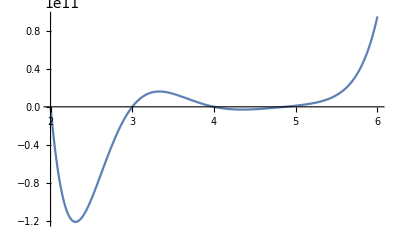

```mathematica
Plot[chromaticPolynomial[10],{q,2,6}]
```

```mathematica
Plot[chromaticPolynomial[20],{q,-0.1,11}]
```

-Graphics-

### Complex Plot of Polynomials

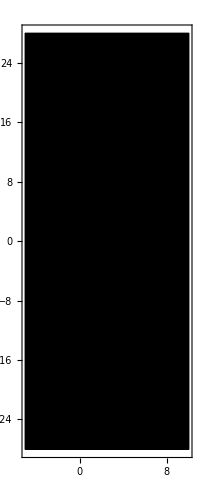

```mathematica
ComplexPlot[chromaticPolynomial[20],{q,-5-28I,10+28I},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic]
```